# Predicting Fractal Dimension with Machine Learning

## By Aubhro Sengupta

## Training set

### Wikipedia

```mathematica
fractalData
```

<|-Graphics-→0.6309,-Graphics-→1,-Graphics-→1.0812,-Graphics-→1.0933,-Graphics-→1.12915,-Graphics-→1.2,-Graphics-→1.2083,-Graphics-→1.2108,-Graphics-→1.2619,-Graphics-→1.2619,-Graphics-→1.2619,-Graphics-→1.2683,-Graphics-→1.328,-Graphics-→1.3057,-Graphics-→1.3934,-Graphics-→1.4649,-Graphics-→1.4649,-Graphics-→1.5,-Graphics-→1.5,-Graphics-→1.5236,-Graphics-→1.5849,-Graphics-→1.61803,-Graphics-→1.6379,-Graphics-→1.6667,-Graphics-→1.7,-Graphics-→1.7227,-Graphics-→1.7712,-Graphics-→1.7848,-Graphics-→1.8687,-Graphics-→1.8617,-Graphics-→1.8928,-Graphics-→1.974,-Graphics-→1.934|>

### Random Julia set

```mathematica
juliaFractals=CreateJuliaFractals[200];
```

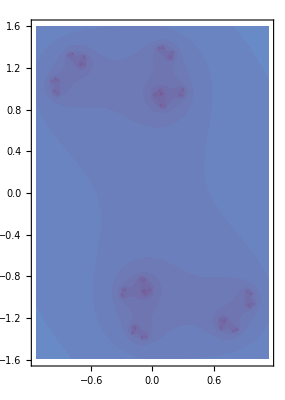
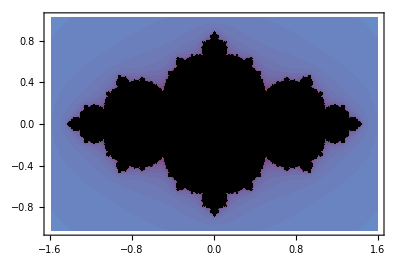
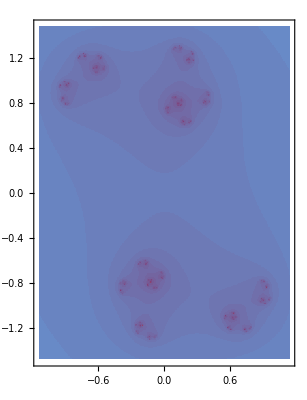
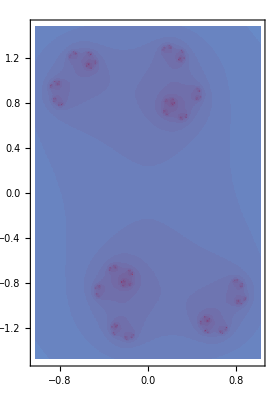
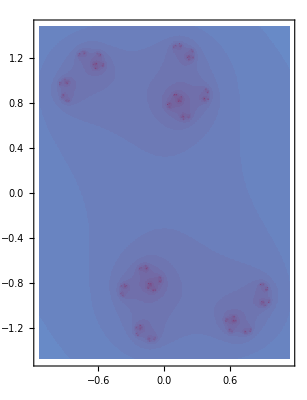
<|-Graphics-→1.16644,-Graphics-→1.273,-Graphics-→1.00955,-Graphics-→1.07399,-Graphics-→1.15547,-Graphics-→1.14594,-Graphics-→1.17243,-Graphics-→1.09533,-Graphics-→1.06663,-Graphics-→1.00477|>

```mathematica
RandomSample[juliaFractals,10]
```

## Evaluation

```mathematica
PredictFractalDimension[fractalData∪juliaFractals,10]
```

{-Graphics-→{1.00234,1.00205,0.000286439},-Graphics-→{1.07399,1.21343,-0.129829},-Graphics-→{1.03947,1.0643,-0.0238845},-Graphics-→{1.0212,1.02709,-0.00577294},-Graphics-→{1.16087,1.13659,0.0209167},-Graphics-→{1.15249,1.15776,-0.00456924},-Graphics-→{1.01748,1.02044,-0.00290468},-Graphics-→{1.05128,1.06585,-0.0138632},-Graphics-→{1.08051,1.08551,-0.00462788},-Graphics-→{1.18803,1.14708,0.0344747}}